```mathematica
sol=NDSolve[{F'''[ξ]+F[ξ]/2 F''[ξ]==0,F[0]==0,F'[0]==0,F''[0]==1},F,{ξ,0,10}][[1]]
```

{F→InterpolatingFunction[…]}

```mathematica
XXX=0.35;halfh=0.01;
```

```mathematica
α=0.332;Vinf=1;ν=0.001;
```

```mathematica
f[η_]:=α^(1/3)F[α^(1/3) η]/.sol
```

```mathematica
ψ[x_,y_]:=f[y  √(Vinf/(ν x))] √(ν x Vinf);
```

```mathematica
Vx[x_,y_]:=(ψ[x,y +0.001]-ψ[x,y ])/0.001
```

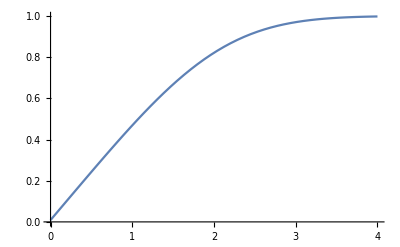

```mathematica
FigBlas=Plot[Evaluate[Vx[x,y  √(2x ν)]]/.x->XXX,{y,0,4}]
```

```mathematica
ω[x_,y_]:=(Vx[x,y+0.0001]-Vx[x,y])/0.0001
```

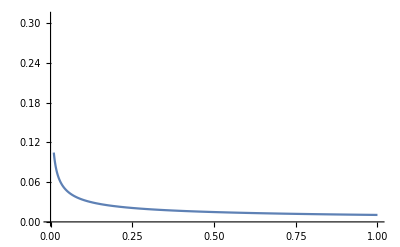

```mathematica
Plot[ν ω[x,0.001],{x,0.01,1},PlotRange->{0,0.31}]
```

```mathematica
Clear[ypod]
```

```mathematica
ypod[x_]:=Flatten[Solve[#,y]&/@Thread[(y /√(2x ν))==Range[0,4,0.08]],1];
tabl[x_]:={x-0.5,(y/.#)+halfh}&/@ypod[x];
```

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Temp\VM2D-21-10\build\blasius

```mathematica
flatTabl=Flatten[tabl[#]&/@{0.35,0.5,0.65},1]
```

{{-0.15,0.01},{-0.15,0.0121166},{-0.15,0.0142332},{-0.15,0.0163498},{-0.15,0.0184664},{-0.15,0.020583},{-0.15,0.0226996},{-0.15,0.0248162},{-0.15,0.0269328},{-0.15,0.0290494},{-0.15,0.031166},{-0.15,0.0332826},{-0.15,0.0353992},{-0.15,0.0375158},{-0.15,0.0396324},{-0.15,0.041749},{-0.15,0.0438656},{-0.15,0.0459822},{-0.15,0.0480988},{-0.15,0.0502154},{-0.15,0.052332},{-0.15,0.0544486},{-0.15,0.0565652},{-0.15,0.0586818},{-0.15,0.0607984},{-0.15,0.062915},{-0.15,0.0650316},{-0.15,0.0671482},{-0.15,0.0692648},{-0.15,0.0713814},{-0.15,0.073498},{-0.15,0.0756146},{-0.15,0.0777312},{-0.15,0.0798478},{-0.15,0.0819644},{-0.15,0.084081},{-0.15,0.0861976},{-0.15,0.0883142},{-0.15,0.0904308},{-0.15,0.0925474},{-0.15,0.094664},{-0.15,0.0967806},{-0.15,0.0988972},{-0.15,0.101014},{-0.15,0.10313},{-0.15,0.105247},{-0.15,0.107364},{-0.15,0.10948},{-0.15,0.111597},{-0.15,0.113713},{-0.15,0.11583},{0.,0.01},{0.,0.0125298},{0.,0.0150596},{0.,0.0175895},{0.,0.0201193},{0.,0.0226491},{0.,0.0251789},{0.,0.0277088},{0.,0.0302386},{0.,0.0327684},{0.,0.0352982},{0.,0.037828},{0.,0.0403579},{0.,0.0428877},{0.,0.0454175},{0.,0.0479473},{0.,0.0504772},{0.,0.053007},{0.,0.0555368},{0.,0.0580666},{0.,0.0605964},{0.,0.0631263},{0.,0.0656561},{0.,0.0681859},{0.,0.0707157},{0.,0.0732456},{0.,0.0757754},{0.,0.0783052},{0.,0.080835},{0.,0.0833648},{0.,0.0858947},{0.,0.0884245},{0.,0.0909543},{0.,0.0934841},{0.,0.096014},{0.,0.0985438},{0.,0.101074},{0.,0.103603},{0.,0.106133},{0.,0.108663},{0.,0.111193},{0.,0.113723},{0.,0.116253},{0.,0.118782},{0.,0.121312},{0.,0.123842},{0.,0.126372},{0.,0.128902},{0.,0.131431},{0.,0.133961},{0.,0.136491},{0.15,0.01},{0.15,0.0128844},{0.15,0.0157689},{0.15,0.0186533},{0.15,0.0215378},{0.15,0.0244222},{0.15,0.0273066},{0.15,0.0301911},{0.15,0.0330755},{0.15,0.03596},{0.15,0.0388444},{0.15,0.0417289},{0.15,0.0446133},{0.15,0.0474977},{0.15,0.0503822},{0.15,0.0532666},{0.15,0.0561511},{0.15,0.0590355},{0.15,0.0619199},{0.15,0.0648044},{0.15,0.0676888},{0.15,0.0705733},{0.15,0.0734577},{0.15,0.0763421},{0.15,0.0792266},{0.15,0.082111},{0.15,0.0849955},{0.15,0.0878799},{0.15,0.0907643},{0.15,0.0936488},{0.15,0.0965332},{0.15,0.0994177},{0.15,0.102302},{0.15,0.105187},{0.15,0.108071},{0.15,0.110955},{0.15,0.11384},{0.15,0.116724},{0.15,0.119609},{0.15,0.122493},{0.15,0.125378},{0.15,0.128262},{0.15,0.131147},{0.15,0.134031},{0.15,0.136915},{0.15,0.1398},{0.15,0.142684},{0.15,0.145569},{0.15,0.148453},{0.15,0.151338},{0.15,0.154222}}

```mathematica
Export["points.txt",flatTabl]
```

points.txt

```mathematica
ptsControl=Cases[flatTabl,{x_/;Abs[(x-(-0.5+XXX))]<10^-4,y_}];
```

```mathematica
ys=Cases[flatTabl,{x_/;Abs[(x-(-0.5+XXX))]<10^-4,y_}:>y];
```

```mathematica
posPtsControl=Flatten[Position[flatTabl,#]&/@ptsControl]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51}

```mathematica
FromFile[pt_]:=Import["velPres/VP-atPoint-"<>If[pt<10,"0",""]<>ToString[pt]<>".csv"][[40;;,3]]
```

```mathematica
Vxs=Mean[FromFile[#-1]]&/@posPtsControl;
```

```mathematica
Max[Vxs]
```

1.05865

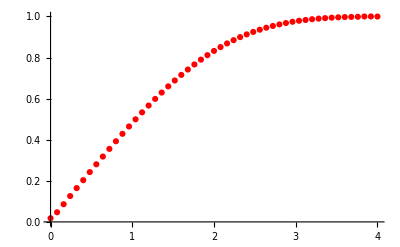

```mathematica
FigMy=ListPlot[Transpose[{Evaluate[(ys-halfh)/√(2x ν)/.x->XXX],Vxs/Max[Vxs]}],PlotStyle->Red]
```

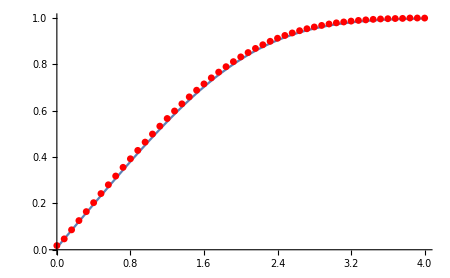

```mathematica
Show[FigBlas,FigMy]
```